```mathematica
h[r_,th_]:=2/Pi*ArcCos[r/th]-2/Pi*r/th*Sqrt[1-(r/th)^2]/;0<=r<=th
h[r_,th_]:=2/Pi*ArcCos[-r/th]+2/Pi*r/th*Sqrt[1-(r/th)^2]/;0>r>-th
h[r_,th_]:=0/;r>th
h[r_,th_]:=0/;r<-th
```

```mathematica
dh[r_,th_]:=-3/2/th+3*0.5/th*(r/th)^2/;0<r<=th
dh[r_,th_]:=+3/2/th-3*0.5/th*(r/th)^2/;0>=r>=-th
dh[r_,th_]:=0/;r>th
```

```mathematica
ddh[r_,th_]:=3*r/th^3/;0<r<=th
ddh[r_,th_]:=-3*r/th^3/;0>=r>=-th
ddh[r_,th_]:=0/;r>th
```

```mathematica
Clear [ddh]
```

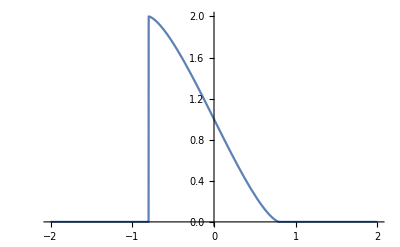

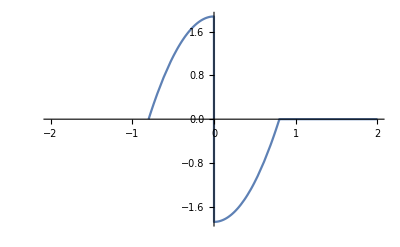

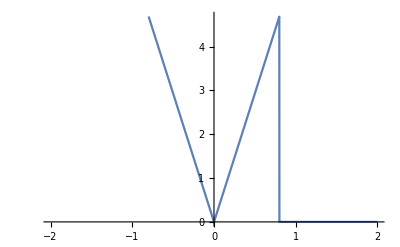

```mathematica
Plot[h[r,0.8],{r,-2,2}]
Plot[dh[r,0.8],{r,-2,2}]
Plot[ddh[r,0.8],{r,-2,2}]
```